# Making High Quality 3D Prints

Math 250 - Math with Mathematica
Christopher Hanusa

## 12.1 Overview

In this tutorial, we export 3D printable models from Mathematica, learn how to make models with higher resolution, and work directly with mesh-based data structures.

## 12.2 Export-Import

First, we’ll see how easy it is to export a model for 3D printing.

### Exporting is easy.

It is very easy to export from Mathematica into many different file types.  Use the command Export!

```mathematica
?Export
```

Here is a 3D zigzag example we’ve seen before:

```mathematica
pointlist={{0,0,0},{1,1,0},{2,0,0},{3,1,0},{4,0,0},{5,1,0},{6,0,0},{7,1,0},{8,0,0}};
zigzag=Graphics3D[Tube[pointlist,.2]]
```

-Graphics3D-

Because we’ve named the object above, we can just include it in this command here.

```mathematica
Export[NotebookDirectory[]<>"zigzag.png",zigzag]
```

C:\Users\chanusa\Dropbox\Web\2017\courses\250\20\mma\zigzag.png

The extension of the file that you use tells Mathematica which file format you want to export to.  Here we’ve exported a PNG file which is an image file and can easily be imported into a be directly inserted .

The NotebookDirectory[] code chooses the folder that our current file is saved in.  The <> (“less-than”-“greater-than”) appends the name of your file to the text string of the current directory.  This helps to keep your files organized.

And then you can see what you’ve exported using Import.

```mathematica
Import[NotebookDirectory[]<>"zigzag.png"]
```

-Graphics-

This imported object is an image.  This means we can’t rotate it or add to it anymore, but we could do some image processing if we wanted to.

### Exporting is not easy.

When you want to create a 3D-printable model, you will want to export it to one of the 3D model types, such as STL.

```mathematica
Export[NotebookDirectory[]<>"tubetest.stl",zigzag]
```

C:\Users\chanusa\Dropbox\Web\2017\courses\250\20\mma\tubetest.stl

```mathematica
Import[NotebookDirectory[]<>"tubetest.stl"]
```

-Graphics3D-

Spin it around - Do you notice anything?

The 3D rendering in Mathematica is not the same as what is exported to the STL file by default.  There are some commands that export well and others that do not export at all!  So as you learn what works and what doesn’t, you will want to export your model to an STL file and re-import it to check that the exported file has the structure you want.

For example, to fix our zigzag structure, we’ll need to add spheres of the same radius as our tube.  Use Map to create them all at once!  Let’s add colors to be able to see the different parts.

```mathematica
spheres=Map[Sphere[#,.2]&,pointlist]
segments=Tube[pointlist,.2]
newZig=Graphics3D[{Blue,segments,Red,spheres}]
```

{Sphere[{0,0,0},0.2],Sphere[{1,1,0},0.2],Sphere[{2,0,0},0.2],Sphere[{3,1,0},0.2],Sphere[{4,0,0},0.2],Sphere[{5,1,0},0.2],Sphere[{6,0,0},0.2],Sphere[{7,1,0},0.2],Sphere[{8,0,0},0.2]}

Tube[{{0,0,0},{1,1,0},{2,0,0},{3,1,0},{4,0,0},{5,1,0},{6,0,0},{7,1,0},{8,0,0}},0.2]

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"newZig.stl",newZig]
```

C:\Users\chanusa\Dropbox\Web\2017\courses\250\20\mma\newZig.stl

```mathematica
Import[NotebookDirectory[]<>"newZig.stl"]
```

-Graphics3D-

### Exporting in color

The STL format does not support color, so we’ll want to use another format (like X3D or WRL) if we want to have a 3D model with some color.

```mathematica
colorZig=Graphics3D[{Red,segments,Blue, spheres}]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"colorZig.x3d",colorZig]
```

C:\Users\chanusa\Dropbox\Web\2017\courses\250\20\mma\colorZig.x3d

```mathematica
Export[NotebookDirectory[]<>"colorZig.wrl",colorZig]
```

C:\Users\chanusa\Dropbox\Web\2017\courses\250\20\mma\colorZig.wrl

Unfortunately Mathematica won’t import these formats.

```mathematica
Import[NotebookDirectory[]<>"colorZig.x3d"]
Import[NotebookDirectory[]<>"colorZig.wrl"]
```

Import::fmtnosup: X3D is not a supported Import format.

$Failed

Import::fmtnosup: VRML is not a supported Import format.

$Failed

To verify that the exporting has worked correctly, we need to use an external viewer to see the models. An online service is Sketchfab.  You can create an account for education using your QC email. Alternatively, you can upload your models directly to the 3D printing service Shapeways and view them there.

## 12.3 Creating smoother curves and surfaces

When you use one of the plotting commands (like Plot3D, ParametricPlot3D, or RegionPlot3D), use the PlotPoints option to increase the resolution of your model.  It changes the number of points that Mathematica uses to approximate your model.  A larger value increases the resolution, but don’t make it too large or it will increase your computation time and result in a very large file.

### Smoother curves

```mathematica
curve=ParametricPlot3D[{Sin[t],Sin[2t],Sin[3t]},{t,0,2Pi},PlotStyle->Tube[.1],PlotRange->All]
```

-Graphics3D-

```mathematica
Import[Export[NotebookDirectory[]<>"Curve.stl",curve]]
```

-Graphics3D-

Make the tube smoother by adding in PlotPoints options into both the ParametricPlot3D function (for the number of points chosen along the curve) and the PlotStyle option (for the number of points chosen on each circular cross-section).  Notice how much longer it takes to process!

```mathematica
curveHD=ParametricPlot3D[{Sin[t],Sin[2t],Sin[3t]},{t,0,2Pi},PlotStyle->Tube[.1,PlotPoints->50],PlotRange->All,PlotPoints->100]
```

-Graphics3D-

```mathematica
Import[Export[NotebookDirectory[]<>"Curve.HD.stl",curveHD]]
```

-Graphics3D-

### Smoother surfaces

To improve the resolution of our torus, use a PlotPoints option.

```mathematica
torus=ParametricPlot3D[{(3+Cos[v]) Cos[u],(3+Cos[v]) Sin[u],Sin[v]},{u,0,2Pi},{v,0,2Pi},PlotStyle->Green,Mesh->None,PlotPoints->30]
```

-Graphics3D-

```mathematica
Import[Export[NotebookDirectory[]<>"Torus.stl",torus]]
```

-Graphics3D-

```mathematica
btorus=ParametricPlot3D[{(3+Cos[v]) Cos[u],(3+Cos[v]) Sin[u],Sin[v]},{u,0,2Pi},{v,0,2Pi},PlotStyle->Green,Mesh->None,PlotPoints->{80,80}]
```

-Graphics3D-

```mathematica
Import[Export[NotebookDirectory[]<>"Torus.HD.stl",btorus]]
```

-Graphics3D-

### Smoother three-dimensional objects

Here is a block that has a bumpy surface.

```mathematica
block=RegionPlot3D[Sin[x]+Sin[y]>z,{x,0-Pi/2,6Pi-Pi/2},{y,0-Pi/2,6Pi-Pi/2},{z,-3,3},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Import[Export[NotebookDirectory[]<>"Bumpy.stl",block]]
```

-Graphics3D-

That’s not nearly as smooth as we would like it, because Mathematica is not sampling many points in each direction.  We can specify the number of points sampled in each direction using the PlotPoints option.

```mathematica
block2=RegionPlot3D[Sin[x]+Sin[y]>z,{x,0-Pi/2,6Pi-Pi/2},{y,0-Pi/2,6Pi-Pi/2},{z,-3,3},PlotPoints->{100,100,100},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
Import[Export[NotebookDirectory[]<>"Bumpy.HD.stl",block2]]
```

-Graphics3D-

## 12.4 Meshes

### An Imperfect World

Mathematica uses mesh-based geometric regions to make three-dimensional objects 3D printable. It is another example of a theoretical object being represented in a human-usable format, similar to how complex numerical expressions can be converted to a decimal or a two-dimensional scene can be represented as a collection of pixels:

```mathematica
Sqrt[Sqrt[3]+5]
```

√(5+√3)

```mathematica
N[√(5+√3)]
```

2.59462

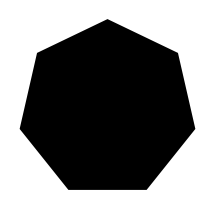

```mathematica
heptagon=Graphics[{RegularPolygon[7]}]
```

```mathematica
Row@{Rasterize[heptagon,ImageSize->50],Rasterize[heptagon,ImageSize->100],Rasterize[heptagon,ImageSize->200]}
```

-Graphics--Graphics--Graphics-

### Boundary Representation vs. Cell Representation

The process of replacing an ideal object by an approximation is called discretization (or triangulation).  This replaces the smooth object by a discrete object made up of cells: points, line segments, triangles, tetrahedra, and higher-dimensional simplices. There are two main ways to describe a discretized object: either by the solid cells that comprise it or by its boundary cells.  Compare the following two discretizations of the circle:

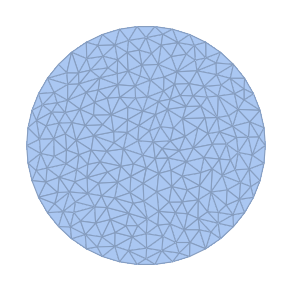
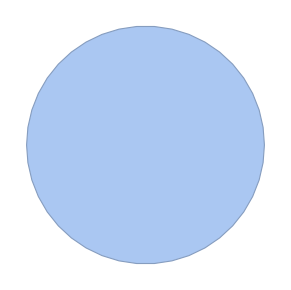

```mathematica
{DiscretizeRegion[Disk[]],BoundaryDiscretizeRegion[Disk[]]}
```

In the first example, the circle is approximated by a collection of two-dimensional triangles. In the second example, the circle is approximated as the interior of a collection of one-dimensional line segments.

Similarly, a sphere can be represented as a collection of three-dimensional tetrahedra or as the interior of a collection of two-dimensional triangles.

```mathematica
{DiscretizeRegion[Ball[]],BoundaryDiscretizeRegion[Ball[]]}
```

{-Graphics3D-,-Graphics3D-}

You can’t see the difference here but we can understand it better by accessing the information directly using MeshPrimitives:

```mathematica
Length@MeshPrimitives[DiscretizeRegion[Ball[]],3]
```

9197

```mathematica
MeshPrimitives[DiscretizeRegion[Ball[]],3][[1;;5]]
Graphics3D[{%,Opacity[.1],Sphere[]}]
```

{Tetrahedron[{{-0.404538,0.914292,0.020458},{-0.447169,0.673185,0.0424964},{-0.499518,0.865043,-0.0467117},{-0.375427,0.75381,-0.121867}}],Tetrahedron[{{0.53354,0.625769,0.197199},{0.479039,0.42215,0.264618},{0.421954,0.560628,0.301252},{0.423007,0.437961,0.130772}}],Tetrahedron[{{0.202236,0.452529,-0.417536},{0.22709,0.594589,-0.300883},{0.105158,0.606749,-0.376721},{0.106578,0.422595,-0.303575}}],Tetrahedron[{{0.226319,0.208791,0.324908},{0.187747,0.239804,0.14349},{0.33788,0.371407,0.228896},{0.344539,0.2026,0.201254}}],Tetrahedron[{{0.465928,0.68706,0.557548},{0.46549,0.464566,0.528497},{0.505115,0.599717,0.620644},{0.354777,0.610145,0.451456}}]}

-Graphics3D-

```mathematica
MeshPrimitives[BoundaryDiscretizeRegion[Ball[]],2][[{100,300,500,700,900}]]
Graphics3D[{%,Opacity[.1],Sphere[]}]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

-Graphics3D-

### The commands

When you are discretizing a shape that is defined as a region, use DiscretizeRegion or BoundaryDiscretizeRegion.  When you are discretizing a shape that is defined as a graphics object, use DiscretizeGraphics or BoundaryDiscretizeGraphics.

### Mesh Notes

The Mathematica developers have been making a lot of progress!

Since boundary representations are one lower dimension than cell representations, they are easier to deal with and have more functionality in Mathematica.  However, not all shapes have a nice boundary representation, in which case you’ll have to work with the shape’s cell representation.

When you use Export, I think Mathematica tries its best to discretize each piece of your model, then combines everything together.  This process sometimes goes awry, so it may make sense to discretize your objects first and then export. For example, Mathematica is able to discretize the zigzag from above without the need to include the spheres.

```mathematica
DiscretizeGraphics[Tube[pointlist,.2]]
```

-Graphics3D-

When you export and import to check the model, you see it is the same and has not lost any parts.

```mathematica
Import[Export[NotebookDirectory[]<>"temp.stl",%]]
```

-Graphics3D-

## 12.5 Creating a smoother mesh

To improve the quality of your discretized region, use the option MaxCellMeasure.

```mathematica
{BoundaryDiscretizeGraphics[Ball[],MaxCellMeasure->.01],
BoundaryDiscretizeGraphics[Ball[],MaxCellMeasure->.001],
BoundaryDiscretizeGraphics[Ball[],MaxCellMeasure->.0001]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{BoundaryDiscretizeGraphics[Graphics3D[Tube[pointlist,.2]],ImageSize->400],
BoundaryDiscretizeGraphics[Graphics3D[Tube[pointlist,.2]],MaxCellMeasure->.0001,ImageSize->400]}
```

{-Graphics3D-,-Graphics3D-}

## 12.6 Creating meshes from images and text

You can discretize images:

Drag and drop your black and white image here.

```mathematica
flower=-Graphics-;
```

Use ImageMesh to discretize.  (ColorNegate is used to convert white pixels to black and vice versa)

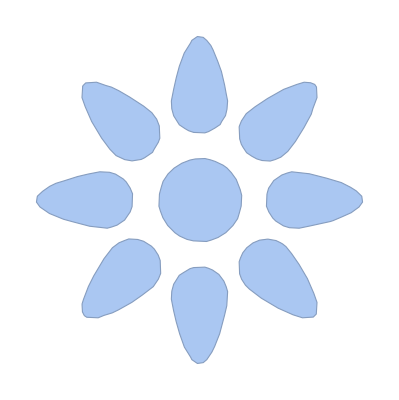

```mathematica
image=ImageMesh[ColorNegate[flower]]
```

You can also discretize words in whatever fonts your computer has installed.

```mathematica
word=Text[Style["word",Bold,FontFamily->"Bauhaus 93",FontSize->50]]
```

word

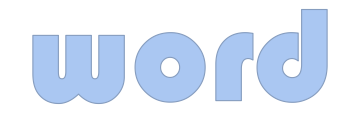

```mathematica
text=BoundaryDiscretizeGraphics[word,_Text]
```

## 12.7 Accessing parts of a mesh

Use MeshCoordinates and MeshPrimitives to get information out of a mesh-based region.  MeshCoordinates will extract the coordinates of the mesh

```mathematica
ball=BoundaryDiscretizeRegion[Ball[]]
```

-Graphics3D-

```mathematica
coords=MeshCoordinates[ball];
```

```mathematica
first10=Take[coords,10]
```

{{-0.607062,0.,0.794654},{0.894427,0.,0.447214},{0.,0.,1.},{-0.723607,-0.525731,0.447214},{-0.723607,0.525731,0.447214},{0.,0.,-1.},{0.276393,-0.850651,0.447214},{0.276393,0.850651,0.447214},{-0.187592,-0.57735,0.794654},{-0.187592,0.57735,0.794654}}

```mathematica
Graphics3D[Map[Point,coords]]
```

-Graphics3D-

Use MeshPrimitives will extract other parts of the object, like its edges or polygonal faces.  The second input is the dimension of the parts you want to extract.

```mathematica
edges=MeshPrimitives[ball,1];  (* edges have dimension 1 *)
```

```mathematica
first10=Take[edges,10]
```

{Line[{{0.276393,-0.850651,0.447214},{0.204995,-0.829094,0.520174}}],Line[{{0.204995,-0.829094,0.520174},{0.185096,-0.890336,0.415981}}],Line[{{0.185096,-0.890336,0.415981},{0.276393,-0.850651,0.447214}}],Line[{{0.204995,-0.829094,0.520174},{0.108274,-0.865931,0.488303}}],Line[{{0.108274,-0.865931,0.488303},{0.185096,-0.890336,0.415981}}],Line[{{0.108274,-0.865931,0.488303},{0.0871575,-0.92155,0.378351}}],Line[{{0.0871575,-0.92155,0.378351},{0.185096,-0.890336,0.415981}}],Line[{{0.108274,-0.865931,0.488303},{0.00617257,-0.893503,0.449014}}],Line[{{0.00617257,-0.893503,0.449014},{0.0871575,-0.92155,0.378351}}],Line[{{0.00617257,-0.893503,0.449014},{-0.0143242,-0.942084,0.33507}}]}

```mathematica
Graphics3D[edges]
```

-Graphics3D-

```mathematica
faces=MeshPrimitives[ball,2];  (* faces have dimension 2 *)
```

```mathematica
first10=Take[faces,100]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
Graphics3D[first10]
```

-Graphics3D-

```mathematica
Graphics3D[faces]
```

-Graphics3D-

## 12.8 Region properties

```mathematica
mesh=PolyhedronData["SnubCube","MeshRegion"]
```

-Graphics3D-

There are two useful commands to situate your object in 3D space. RegionBounds lets you know the size of the object by giving the lower and upper bounds of the x, y, and z variables for all points in the object. RegionCentroid gives the center of mass of the object.

Here we see that the size of this object is 2.29 units wide and is centered at (0,0,0):

```mathematica
RegionBounds[mesh]
Map[#[[2]]-#[[1]]&,%]
```

{{-1.14261,1.14261},{-1.14261,1.14261},{-1.14261,1.14261}}

{2.28523,2.28523,2.28523}

```mathematica
RegionCentroid[mesh]
```

{-9.32283×10^-17,-8.44332×10^-17,-4.04576×10^-17}

```mathematica
Chop[RegionCentroid[mesh]]
```

{0,0,0}

```mathematica
Total[{0,0,0}]
```

0

## 12.9 Changing the size of the Region

There is an easy way to change the size of a model when it is a mesh-based region---use RegionResize.  If you only use one parameter as the second input, it will scale the object to have first coordinate equal to that input.  If you specify a list of parameters, it will scale the object to fit into the given box, not respecting the ratios between side lengths.

If we want our model to be 100 units wide, we would write:

```mathematica
newmesh=RegionResize[mesh, 100]
```

-Graphics3D-

```mathematica
RegionBounds[newmesh]
```

{{-50.,50.},{-50.,50.},{-50.,50.}}

If we want to skew it differently in each direction, we can do this:

```mathematica
skewmesh=RegionResize[mesh, {10,1,2}]
```

-Graphics3D-

```mathematica
RegionBounds[skewmesh]
```

{{-5.,5.},{-0.5,0.5},{-1.,1.}}

When you are finalizing your model, you will have a 3D rendering of your object that you created using coordinates with dimensions determined by mathematical units. Once you have exported your model and re-imported your model to make sure that the form is correct, you will need to scale your model to be in millimeters before you upload to Shapeways.  For instance, the model that was 100 units will be 100 mm (approximately 4 inches) when printed by the 3D printer.  As you change the size of your model, the price of your 3D print is impacted.  So you will want to play around with the sizing and do a cost-benefit analysis to determine the final size of your model.

## 12.10 Translations and Rotations

If you want to perform a transformation on a region, use TransformedRegion and the various Transform commands.

For example, we can apply various transformations to the basic cube:

```mathematica
cube=BoundaryDiscretizeGraphics[Cuboid[]];
Graphics3D[{Green,cube},Axes->True,Boxed->True,AxesLabel->{"x","y","z"}, ImageSize->150,PlotRange->All]
```

-Graphics3D-

To rotate the object by a given angle θ around an axis of rotation (with direction v and passing through point p), input these values into RotationTransform.

```mathematica
rotated=TransformedRegion[cube,RotationTransform[Pi/4,{0,0,1},{1/2,1/2,1/2}]];
Graphics3D[{{Opacity[.4],Green,cube},{Red,rotated}},Axes->True,Boxed->True,AxesLabel->{"x","y","z"}, ImageSize->300,PlotRange->All]
```

-Graphics3D-

To translate the object along a vector v, input that vector into TranslationTransform.

```mathematica
translated=TransformedRegion[cube,TranslationTransform[{1,1,0}]];
Graphics3D[{{Opacity[.4],Green,cube},{Red,translated}},Axes->True,Boxed->True,AxesLabel->{"x","y","z"}, ImageSize->300,PlotRange->All]
```

-Graphics3D-

Combining a few of these techniques is useful to reset the position of an object.

Example 12.10.1. Create a region shaped like Germany that is centered at the origin and 2 inches across.

{{-0.0343695,0.0659039},{-0.0649757,0.0708395}}

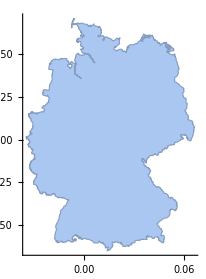

```mathematica
germany=BoundaryDiscretizeGraphics[CountryData["Germany","Shape"]];
RegionBounds[germany]
Show[germany,Axes->True]
```

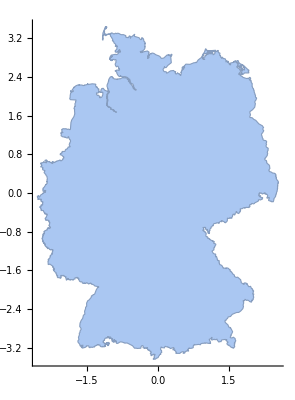

```mathematica
imagereset=RegionResize[TransformedRegion[germany,TranslationTransform[-RegionCentroid[germany]]],2*2.54];
Show[imagereset,Axes->True]
```

## 12.11 Region boolean operations

RegionIntersection, RegionUnion, and RegionDifference are used to intersect, merge, or subtract two regions.  These commands work well in 2D. RegionIntersection and RegionDifference do not often work for 3D cell representations.  (But starting in version 12.1 of Mathematica, they do work more often for 3D boundary representations!)

### 2D Examples

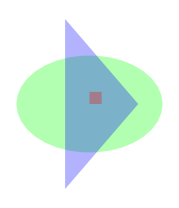

```mathematica
ovalmesh=DiscretizeGraphics[Graphics[Disk[{0,0},{6,4}]]];
trianglemesh=DiscretizeGraphics[Graphics[Polygon[{{-2,-7},{-2,7},{4,0}}]]];
squaremesh=DiscretizeGraphics[Graphics[Polygon[{{0,0},{0,1},{1,1},{1,0}}]]];
Graphics[{Opacity[.3],Green,ovalmesh,Blue,trianglemesh,Red,squaremesh}]
```

The union of the oval and the triangle:

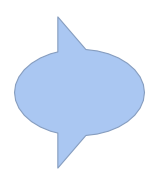

```mathematica
RegionUnion[ovalmesh,trianglemesh]
```

The intersection of the oval and the triangle:

```mathematica
RegionIntersection[ovalmesh,trianglemesh]
```

-Graphics-

The oval with the square removed:

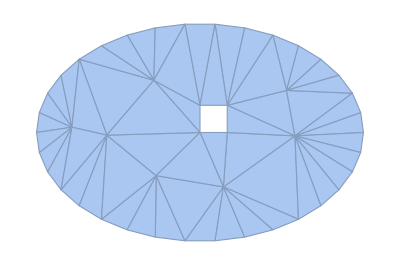

```mathematica
RegionDifference[ovalmesh,squaremesh]
```

### 3D Boundary Mesh Examples

```mathematica
ball=BoundaryDiscretizeGraphics[Graphics3D[Ball[{0,0,0},1]]];
cube=BoundaryDiscretizeGraphics[Graphics3D[Cuboid[{0.1,0.1,0.1},{1,1,1}]]];
tetrahedron=BoundaryDiscretizeGraphics[PolyhedronData["Tetrahedron","Polyhedron"]];
Graphics3D[{Opacity[.3],Green,ball,Blue,cube,Red,tetrahedron}]
```

-Graphics3D-

Here you can see that you can make the union of two 3D meshes, but the intersection and the difference don’t  work

```mathematica
{RegionUnion[ball,cube],RegionUnion[tetrahedron,cube]}
{RegionIntersection[ball,cube],RegionDifference[ball,cube],RegionDifference[tetrahedron,cube]}
```

{-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

### 3D Region Mesh Examples

```mathematica
ball=DiscretizeGraphics[Graphics3D[Sphere[{0,0,0},1]]];
cube=DiscretizeGraphics[Graphics3D[Cuboid[{0,0,0},{1,1,1}]]];
tetrahedron=DiscretizeGraphics[PolyhedronData["Tetrahedron","Polyhedron"]];
```

Here you can see that you can make the union of two 3D meshes, but the intersection and the difference don’t  work

```mathematica
{RegionUnion[ball,cube],RegionUnion[tetrahedron,cube]}
{RegionIntersection[ball,cube],RegionDifference[ball,cube],RegionDifference[tetrahedron,cube]}
```

{-Graphics3D-,-Graphics3D-}

{BooleanRegion[#1&&#2&,{-Graphics3D-,-Graphics3D-}],BooleanRegion[#1&&!#2&,{-Graphics3D-,-Graphics3D-}],-Graphics3D-}